## Rosenbrock in ℝ^30

With the default value of the constant and n=30.    

Out of 10000 runs FindMinimum finds: 
	* the global min about 88% of the time;
	* the local min about 10% of the time;
	* finds single hump saddles the rest of the time. 
I find the global min

```mathematica
1142/10000.
```

0.1142

```mathematica
Clear[Rosen]
Rosen[n_][x_]:= Sum[
100.0 (x⟦i⟧^2-x⟦i+1⟧)^2+(x⟦i⟧-1)^2,{i,1,n-1}]

n=30;

vars=Array[x,n];
Data={};
Tol=10^-7;
Do[
x0=RandomReal[{-1,1},n];
{val,sub}=Chop[FindMinimum[Rosen[n][vars],{vars,x0}ᵀ]];
If[Abs[val]>Tol,
Data={Data,vars/.sub}],
{10000}]
Data=Sort[Partition[Flatten[Data],n]];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

1159

{1142,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

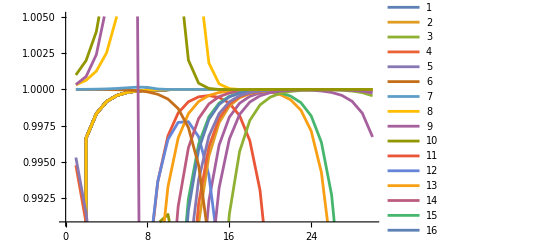

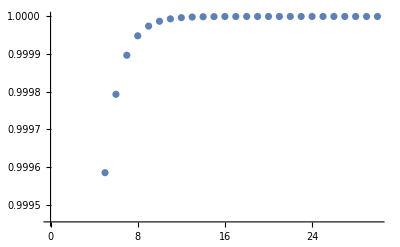

```mathematica
Length[Data]
Hmm=Split[Data,Norm[#1-#2]<10^-7&];
Map[Length,Hmm]
ListPlot[Data⟦1105;;-1⟧,
Joined->True,
PlotLegends->True]
ListPlot[Data⟦1⟧]
```

```mathematica
n=30;

vars=Array[x,n];
Data={};
Tol=10^-7;
Do[
x0=RandomReal[{-1,1},n];
{val,sub}=Chop[FindMinimum[Rosen[n][vars],{vars,x0}ᵀ,Method->"InteriorPoint"]];
If[Abs[val]>Tol,
Data={Data,vars/.sub}],
{1000}]
Data=Sort[Partition[Flatten[Data],n]];
```

```mathematica
Hmm=Split[Data,Norm[#1-#2]<10^-7&];
Map[ Length,Hmm]
Dimensions[Hmm]
ListPlot[Hmm⟦All,6⟧,Joined->True]
```

{70,1,1,6,2,21,9,14,3,1,1,2,3,1,1,1,2,1,2,1,2,2,1,1,3,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{45}

Part::partw: Part 6 of {{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,«20»}} does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression 6 cannot be used as a part specification.

Part::pkspec1: The expression All cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: {{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,«20»},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,«20»},«8»,«60»},«9»,«35»}⟦All,6⟧ is not a list of numbers or pairs of numbers.

ListPlot[{{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999998}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999998}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999997}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999997}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999996},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999996},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999996}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997,0.999995}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997,0.999995}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997,0.999994}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999997,0.999993}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999997,0.999993},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999997,0.999993},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999997,0.999993}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999997,0.999993}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999996,0.999992}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999998,0.999996,0.999992}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999998,0.999995,0.99999}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997,0.999995,0.99999}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997,0.999995,0.999989}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997,0.999994,0.999989}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997,0.999994,0.999988}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999997,0.999993,0.999986}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999998,0.999995,0.999991,0.999982}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999998,0.999995,0.999991,0.999981}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997,0.999995,0.999989,0.999979}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997,0.999995,0.999989,0.999978}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999997,0.999995,0.999989,0.999978}},{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999998,0.999996,0.999993,0.999985,0.999971}}}⟦All,6⟧,Joined→True]

{1835}

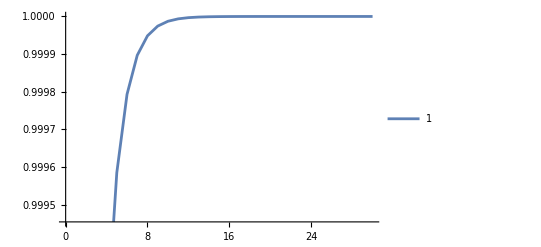

-Graphics-

```mathematica
Map[Length,Hmm]
ListPlot[Data⟦-1⟧,
Joined->True,
PlotLegends->True]
ListPlot[Data⟦1⟧]
```

```mathematica
?Split
```

```mathematica
Data⟦1;;3⟧
```

{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

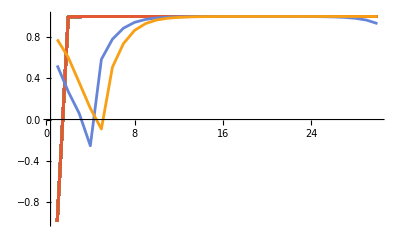

```mathematica
ListPlot[Data,Joined->True,PlotRange->All]
```

```mathematica
Data
```

{{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{-0.993286,0.996651,0.99833,0.999168,0.999585,0.999793,0.999897,0.999949,0.999974,0.999987,0.999994,0.999997,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
vars=Array[x,n];
{val,sub}=FindMinimum[Rosen[n][vars],{vars,x0}]
xMin=x/.sub;
{val,Rosen[n][xMin],xMin-x0}
```

Part::partd: Part specification vars⟦1⟧ is longer than depth of object.

Part::partd: Part specification vars⟦2⟧ is longer than depth of object.

Part::partd: Part specification vars⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{1.18006×10^-24,{{x[1],x[2],x[3],x[4],x[5]}→{1.,1.,1.,1.,1.}}}

Part::partd: Part specification x⟦1⟧ is longer than depth of object.

Part::partd: Part specification x⟦2⟧ is longer than depth of object.

Part::partd: Part specification x⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{1.18006×10^-24,(-1+x⟦1⟧)^2+100. (x⟦1⟧^2-x⟦2⟧)^2+(-1+x⟦2⟧)^2+100. (x⟦2⟧^2-x⟦3⟧)^2+(-1+x⟦3⟧)^2+100. (x⟦3⟧^2-x⟦4⟧)^2+(-1+x⟦4⟧)^2+100. (x⟦4⟧^2-x⟦5⟧)^2,{-0.782971+x,0.471057+x,0.474588+x,-0.1713+x,0.0122641+x}}

```mathematica
?FindMinimum
```

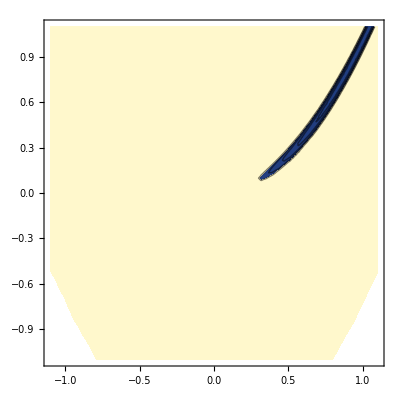

```mathematica
ContourPlot[Rosen[{x1,x2}],{x1,-1.1,1.1},{x2,-1.1,1.1},
Contours->{0.1,0.2,0.3,0.4,0.5}]
```

## Rosenbrock in ℝ^60

With the default value of the constant and n=.    

Out of 10000 runs FindMinimum finds: 
	* the global min about 88% of the time;
	* the local min about 10% of the time;
	* single hump saddles the rest of the time.

```mathematica
Clear[Rosen]
Rosen[n_][x_]:= Sum[
100.0 (x⟦i⟧^2-x⟦i+1⟧)^2+(x⟦i⟧-1)^2,{i,1,n-1}]

n=60;

vars=Array[x,n];
Data={};
Tol=10^-7;
Do[
x0=RandomReal[{-1,1},n];
{val,sub}=Chop[FindMinimum[Rosen[n][vars],{vars,x0}ᵀ]];
If[Abs[val]>Tol,
Data={Data,vars/.sub}],
{10000}]
Data=Sort[Partition[Flatten[Data],n]];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

```mathematica
Length[Data]
```

2286

```mathematica
Length[Data]
Hmm=Sort[Split[Data,Norm[#1-#2]<10^-5&],(Length[#1]>Length[#2])&];
Map[Length,Hmm];
Hmm⟦4,1⟧
Hmm⟦3,1⟧
```

2286

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.00001,1.00002,1.00003,1.00007,1.00012,1.00021,1.00025,0.999797,0.996476}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.00001,1.00001,1.00002,1.00004,1.00008,1.00016,1.00029,1.00048,1.00056,0.999526,0.992994}

```mathematica
Length[Hmm]
```

1108

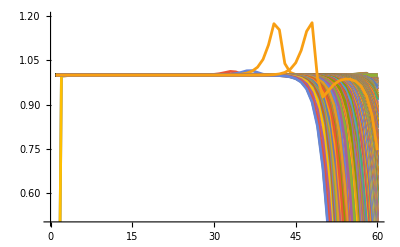

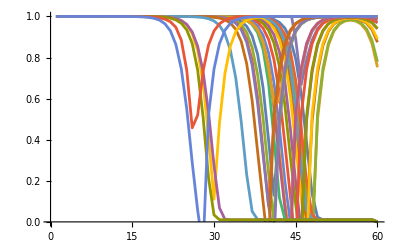

```mathematica
ListPlot[Hmm⟦1;;973,1⟧,
Joined->True,
PlotRange->{0.5,1.2}]
ListPlot[Hmm⟦974;;1000,1⟧,
Joined->True,
PlotRange->{0,1.}]
```